```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[1,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=T1[1,m]},
sl1= Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,2m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[T].J.T].c],4]; J=J]; Il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,1,0,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
tr[0.51,0.0001,1,0,0,7]
```

1.99924

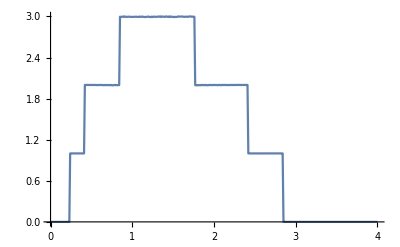

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,0,7]},{ω,Range[0,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp3[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp4[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp5[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp6[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp7[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp8[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp9[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp10[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp11[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp12[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp13[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp14[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*δ-0]]]
```

```mathematica
Clear[set]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_]:=set[ω,δ,t,ϵ,ϵ1,m,num]=RandomSample[Join[RandomChoice[{imp1[ω,δ,t,ϵ,ϵ1,m],imp2[ω,δ,t,ϵ,ϵ1,m],imp3[ω,δ,t,ϵ,ϵ1,m],imp4[ω,δ,t,ϵ,ϵ1,m],imp5[ω,δ,t,ϵ,ϵ1,m],imp6[ω,δ,t,ϵ,ϵ1,m],imp7[ω,δ,t,ϵ,ϵ1,m],imp8[ω,δ,t,ϵ,ϵ1,m],imp9[ω,δ,t,ϵ,ϵ1,m],imp10[ω,δ,t,ϵ,ϵ1,m],imp11[ω,δ,t,ϵ,ϵ1,m],imp12[ω,δ,t,ϵ,ϵ1,m],imp13[ω,δ,t,ϵ,ϵ1,m],imp14[ω,δ,t,ϵ,ϵ1,m]},num],Table[imp[ω,δ,t,ϵ,0,m],100-num]],100]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_,size_]:=Module[{gg=g[ω,δ,t,ϵ,m],x=T1[1,m],T=ρ[1,m]},
η=Module[{cc=set[ω,δ,t,ϵ,ϵ1,m,num]},
sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[14]-cc[[ζ]].ConjugateTranspose[x].J.x].cc[[ζ]],{ζ,1,size}];J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,ϵ,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,m].T.sl1.T].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
η]
```

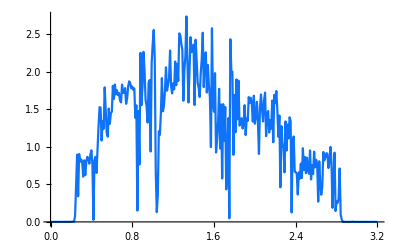

```mathematica
ListLinePlot[Join[Table[{ω,tr1[ω,0.0001,1,0,0.3,7,42,100]},{ω,Range[0,1.76,0.01]}],Table[{ω,If[tr1[ω,0.0001,1,0,0.3,7,42,100]>2,2,tr1[ω,0.0001,1,0,0.3,7,42,100]]},{ω,Range[1.77,2.41,0.01]}],Table[{ω,If[tr1[ω,0.0001,1,0,0.3,7,42,100]>1,1,tr1[ω,0.0001,1,0,0.3,7,42,100]]},{ω,Range[2.42,3.2,0.01]}]],PlotStyle->RGBColor[0.06,0.45,0.98]]
```

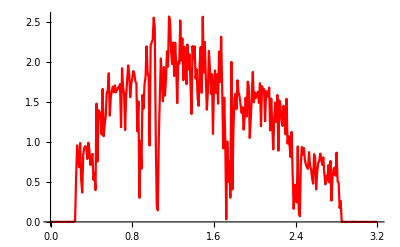

```mathematica
ListLinePlot[Join[Table[{ω,tr1[ω,0.0001,1,0,0.3,7,42,100]},{ω,Range[0,1.76,0.01]}],Table[{ω,If[tr1[ω,0.0001,1,0,0.3,7,42,100]>2,2,tr1[ω,0.0001,1,0,0.3,7,42,100]]},{ω,Range[1.77,2.41,0.01]}],Table[{ω,If[tr1[ω,0.0001,1,0,0.3,7,42,100]>1,1,tr1[ω,0.0001,1,0,0.3,7,42,100]]},{ω,Range[2.42,3.2,0.01]}]],PlotStyle->Red]
```

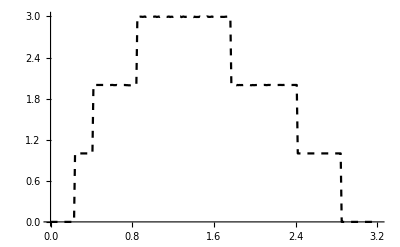

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.0001,1,0,0,7,50,50]},{ω,Range[0,3.2,0.01]}],PlotRange->All,PlotStyle->{Dashed,RGBColor[0,0,0]}]
```

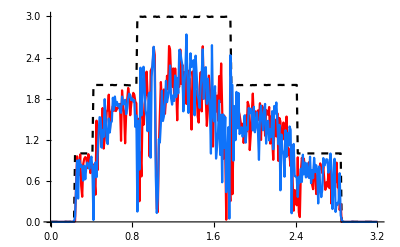

```mathematica
Show[%33,%32,%28,PlotRange->All,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε[t]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

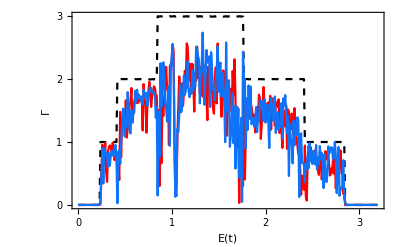

```mathematica
Show[%50,Frame->True,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},Automatic}}]
```

```mathematica
Export["42imp.eps",%51,ImageSize->{500,500}]
```

42imp.eps

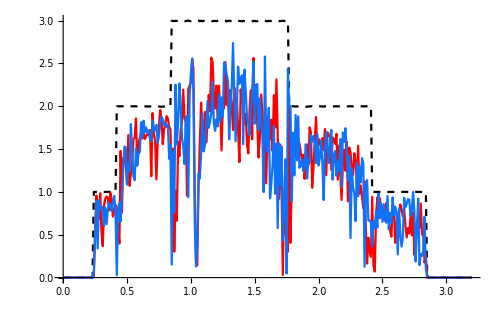

```mathematica
Show[%33,%32,%28,PlotRange->All,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε[t]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

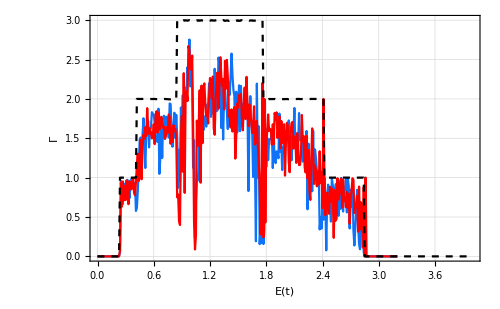

```mathematica
Show[%40,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε[t]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

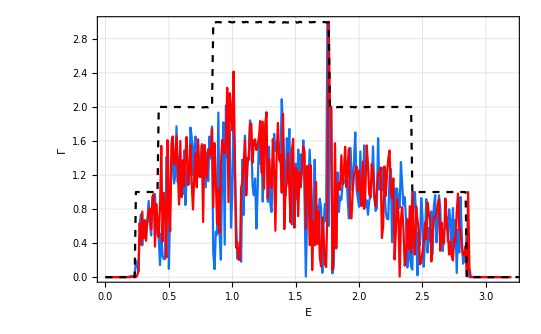

```mathematica
Show[%266,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{14,GrayLevel[0]},ImageResolution->2000]
```

```mathematica
Export["100imp.eps",%268]
```

100imp.eps

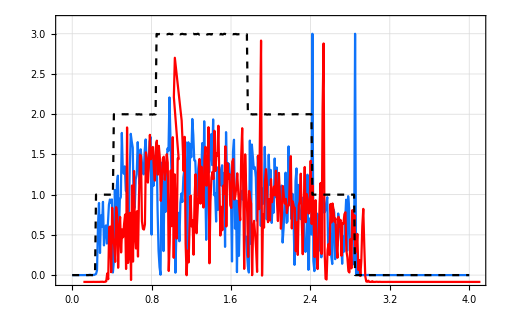

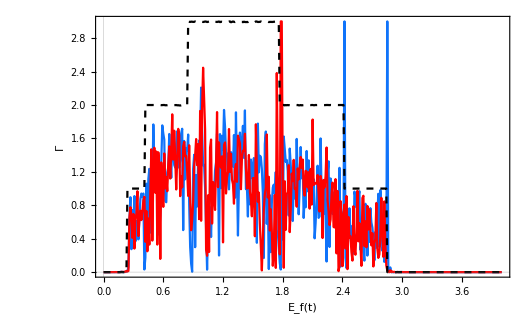

```mathematica
Show[%186,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, f][t]],None}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

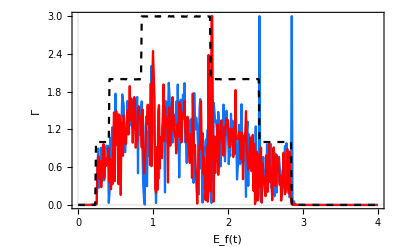

```mathematica
Show[%187,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

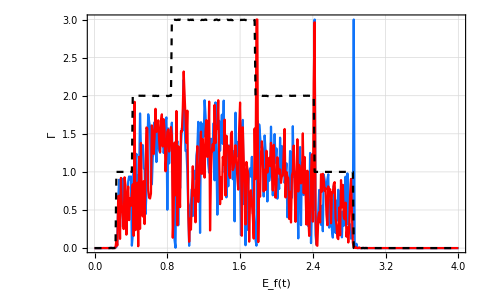

```mathematica
Show[%207,PlotLabel->None,LabelStyle->{12,GrayLevel[0]},FrameLabel->{{HoldForm[Γ],None},{HoldForm[Subscript[Ε, f][t]],None}}]
```

```mathematica
tr50[ω_,ϵ1_]:=Module[{Tin=T1[1,7],T=ρ[1,7],imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},list={(*RandomSample[*){imp,imp14,imp,imp4,imp12,imp8,imp13,imp,imp12,imp,imp2,imp11,imp,imp10,imp,imp,imp,imp10,imp13,imp5,imp2,imp,imp7,imp,imp,imp2,imp,imp,imp,imp5,imp2,imp4,imp13,imp2,imp,imp,imp,imp,imp1,imp,imp8,imp2,imp5,imp,imp11,imp,imp,imp,imp,imp,imp5,imp,imp,imp8,imp,imp,imp5,imp,imp2,imp,imp,imp,imp13,imp2,imp,imp12,imp,imp,imp,imp,imp1,imp,imp,imp,imp10,imp,imp14,imp,imp,imp13,imp,imp2,imp,imp7,imp,imp,imp,imp8,imp9,imp,imp,imp,imp,imp,imp,imp2,imp7,imp8,imp,imp}(*]*)};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,3,7}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
tr50[1,0.5]
```

2.64648

```mathematica
Table[{ω,tr50[ω,0.5]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000171009},{0.01,0.000111989},{0.02,0.0000670223},{0.03,0.0000344746},{0.04,0.0000133243},{0.05,3.10085×10^-6},{0.06,3.86562×10^-6},{0.07,0.0000162382},{0.08,0.0000414711},{0.09,0.0000815875},{0.1,0.000139603},{0.11,0.000219877},{0.12,0.000328648},{0.13,0.000474897},{0.14,0.000671718},{0.15,0.000938623},{0.16,0.00130554},{0.17,0.00182013},{0.18,0.00256219},{0.19,0.00367443},{0.2,0.00543705},{0.21,0.00848335},{0.22,0.0146388},{0.23,0.0333038},{0.24,0.175452},{0.25,0.432117},{0.26,0.559604},{0.27,0.635982},{0.28,0.68578},{0.29,0.719406},{0.3,0.749457},{0.31,0.767621},{0.32,0.781347},{0.33,0.788902},{0.34,0.799012},{0.35,0.792026},{0.36,0.797246},{0.37,0.78488},{0.38,0.75557},{0.39,0.692728},{0.4,0.596641},{0.41,0.197942},{0.42,0.0131167},{0.43,0.697637},{0.44,1.05915},{0.45,1.25556},{0.46,1.39642},{0.47,1.49461},{0.48,1.57718},{0.49,1.62988},{0.5,1.6933},{0.51,1.73194},{0.52,1.76563},{0.53,1.78975},{0.54,1.82188},{0.55,1.84407},{0.56,1.85987},{0.57,1.87686},{0.58,1.89031},{0.59,1.90178},{0.6,1.91461},{0.61,1.9216},{0.62,1.92648},{0.63,1.93185},{0.64,1.92776},{0.65,1.93574},{0.66,1.93787},{0.67,1.93638},{0.68,1.93731},{0.69,1.93206},{0.7,1.93225},{0.71,1.92991},{0.72,1.92239},{0.73,1.91738},{0.74,1.91559},{0.75,1.90638},{0.76,1.90625},{0.77,1.89652},{0.78,1.89477},{0.79,1.89728},{0.8,1.88851},{0.81,1.8727},{0.82,1.86934},{0.83,1.85998},{0.84,1.85587},{0.85,1.8266},{0.86,2.08406},{0.87,2.25599},{0.88,2.3451},{0.89,2.44617},{0.9,2.48667},{0.91,2.4974},{0.92,2.51257},{0.93,2.54171},{0.94,2.56603},{0.95,2.56972},{0.96,2.58606},{0.97,2.59394},{0.98,2.61979},{0.99,2.62627},{1.,2.64648},{1.01,2.66673},{1.02,2.67536},{1.03,2.6343},{1.04,2.43728},{1.05,1.95666},{1.06,1.40818},{1.07,0.947851},{1.08,1.47204},{1.09,1.81194},{1.1,1.98624},{1.11,2.07948},{1.12,2.1451},{1.13,2.22122},{1.14,2.2969},{1.15,2.30728},{1.16,2.3797},{1.17,2.41529},{1.18,2.45447},{1.19,2.47616},{1.2,2.50659},{1.21,2.53114},{1.22,2.58609},{1.23,2.60348},{1.24,2.60673},{1.25,2.66967},{1.26,2.70239},{1.27,2.69303},{1.28,2.74184},{1.29,2.75724},{1.3,2.76533},{1.31,2.77418},{1.32,2.78136},{1.33,2.81157},{1.34,2.83279},{1.35,2.80738},{1.36,2.83764},{1.37,2.81284},{1.38,2.78805},{1.39,2.77869},{1.4,2.78472},{1.41,2.77821},{1.42,2.72473},{1.43,2.72233},{1.44,2.73061},{1.45,2.6928},{1.46,2.6475},{1.47,2.61544},{1.48,2.61951},{1.49,2.61731},{1.5,2.597},{1.51,2.5763},{1.52,2.51594},{1.53,2.53325},{1.54,2.5016},{1.55,2.47786},{1.56,2.45053},{1.57,2.3968},{1.58,2.3741},{1.59,2.3536},{1.6,2.32705},{1.61,2.33876},{1.62,2.32099},{1.63,2.31314},{1.64,2.29457},{1.65,2.24079},{1.66,2.19069},{1.67,2.19464},{1.68,2.1878},{1.69,2.13057},{1.7,2.12175},{1.71,2.03023},{1.72,1.99807},{1.73,1.88637},{1.74,1.75278},{1.75,1.48642},{1.76,0.401676},{1.77,1.21438},{1.78,1.29141},{1.79,1.19678},{1.8,0.647545},{1.81,0.40223},{1.82,1.2173},{1.83,1.47196},{1.84,1.61376},{1.85,1.68651},{1.86,1.71789},{1.87,1.74497},{1.88,1.72239},{1.89,1.80102},{1.9,1.76879},{1.91,1.79925},{1.92,1.82414},{1.93,1.8218},{1.94,1.84148},{1.95,1.885},{1.96,1.86489},{1.97,1.87183},{1.98,1.88456},{1.99,1.91065},{2.,1.92847},{2.01,1.93495},{2.02,1.92888},{2.03,1.94034},{2.04,1.96624},{2.05,1.96012},{2.06,1.97943},{2.07,1.98383},{2.08,1.97957},{2.09,1.98855},{2.1,1.98916},{2.11,1.98963},{2.12,1.98432},{2.13,1.98327},{2.14,1.97784},{2.15,1.9651},{2.16,1.96027},{2.17,1.94724},{2.18,1.93641},{2.19,1.91106},{2.2,1.89475},{2.21,1.8836},{2.22,1.85841},{2.23,1.83751},{2.24,1.82741},{2.25,1.79458},{2.26,1.78387},{2.27,1.74331},{2.28,1.72223},{2.29,1.70136},{2.3,1.67084},{2.31,1.64547},{2.32,1.61463},{2.33,1.56986},{2.34,1.52936},{2.35,1.49754},{2.36,1.43685},{2.37,1.37567},{2.38,1.27263},{2.39,1.14111},{2.4,0.955416},{2.41,0.577654},{2.42,0.650885},{2.43,0.485671},{2.44,0.372248},{2.45,3},{2.46,0.455212},{2.47,0.591676},{2.48,0.818798},{2.49,0.902751},{2.5,0.942502},{2.51,0.963452},{2.52,0.974788},{2.53,0.980536},{2.54,0.983799},{2.55,0.98358},{2.56,0.980855},{2.57,0.97692},{2.58,0.969424},{2.59,0.961505},{2.6,0.950831},{2.61,0.937102},{2.62,0.923508},{2.63,0.907576},{2.64,0.889898},{2.65,0.871761},{2.66,0.853091},{2.67,0.833347},{2.68,0.813041},{2.69,0.792598},{2.7,0.772477},{2.71,0.752823},{2.72,0.734285},{2.73,0.716933},{2.74,0.701107},{2.75,0.687204},{2.76,0.675656},{2.77,0.66685},{2.78,0.66129},{2.79,0.659528},{2.8,0.662148},{2.81,0.669555},{2.82,0.68103},{2.83,0.689972},{2.84,0.645699},{2.85,0.010761},{2.86,0.00136703},{2.87,0.00035698},{2.88,0.0000273927},{2.89,0.00991586},{2.9,0.000535057},{2.91,0.000193945},{2.92,0.0001042},{2.93,0.0000639493},{2.94,0.0000420493},{2.95,0.000028886},{2.96,0.0000204704},{2.97,0.0000148549},{2.98,0.000010986},{2.99,8.25287×10^-6},{3.,6.28214×10^-6},{3.01,4.83669×10^-6},{3.02,3.76091×10^-6},{3.03,2.95007×10^-6},{3.04,2.33209×10^-6},{3.05,1.85641×10^-6},{3.06,1.48703×10^-6},{3.07,1.19788×10^-6},{3.08,9.69889×10^-7},{3.09,7.88935×10^-7},{3.1,6.44437×10^-7},{3.11,5.28404×10^-7},{3.12,4.34749×10^-7},{3.13,3.58793×10^-7},{3.14,2.9692×10^-7},{3.15,2.4631×10^-7},{3.16,2.04755×10^-7},{3.17,1.70512×10^-7},{3.18,1.42202×10^-7},{3.19,1.18724×10^-7},{3.2,9.91964×10^-8},{3.21,8.29121×10^-8},{3.22,6.92982×10^-8},{3.23,5.78909×10^-8},{3.24,4.83122×10^-8},{3.25,4.02535×10^-8},{3.26,3.34615×10^-8},{3.27,2.77282×10^-8},{3.28,2.28816×10^-8},{3.29,1.87796×10^-8},{3.3,1.53041×10^-8},{3.31,1.2357×10^-8},{3.32,9.85624×10^-9},{3.33,7.73332×10^-9},{3.34,5.93078×10^-9},{3.35,4.4003×10^-9},{3.36,3.10124×10^-9},{3.37,1.99928×10^-9},{3.38,1.06541×10^-9},{3.39,2.75055×10^-10},{3.4,3.92631×10^-10},{3.41,9.55372×10^-10},{3.42,1.42826×10^-9},{3.43,1.82415×10^-9},{3.44,2.15404×10^-9},{3.45,2.42732×10^-9},{3.46,2.65204×10^-9},{3.47,2.83508×10^-9},{3.48,2.98237×10^-9},{3.49,3.09899×10^-9},{3.5,3.18932×10^-9},{3.51,3.25712×10^-9},{3.52,3.30563×10^-9},{3.53,3.33766×10^-9},{3.54,3.3556×10^-9},{3.55,3.36156×10^-9},{3.56,3.35731×10^-9},{3.57,3.34443×10^-9},{3.58,3.32425×10^-9},{3.59,3.29794×10^-9},{3.6,3.2665×10^-9},{3.61,3.23079×10^-9},{3.62,3.19157×10^-9},{3.63,3.1495×10^-9},{3.64,3.10511×10^-9},{3.65,3.05891×10^-9},{3.66,3.01131×10^-9},{3.67,2.96266×10^-9},{3.68,2.91327×10^-9},{3.69,2.86342×10^-9},{3.7,2.81332×10^-9},{3.71,2.76317×10^-9},{3.72,2.71314×10^-9},{3.73,2.66336×10^-9},{3.74,2.61396×10^-9},{3.75,2.56503×10^-9},{3.76,2.51667×10^-9},{3.77,2.46893×10^-9},{3.78,2.42187×10^-9},{3.79,2.37555×10^-9},{3.8,2.32999×10^-9},{3.81,2.28523×10^-9},{3.82,2.24129×10^-9},{3.83,2.19818×10^-9},{3.84,2.15592×10^-9},{3.85,2.11451×10^-9},{3.86,2.07395×10^-9},{3.87,2.03424×10^-9},{3.88,1.99538×10^-9},{3.89,1.95736×10^-9},{3.9,1.92018×10^-9},{3.91,1.88382×10^-9},{3.92,1.84827×10^-9},{3.93,1.81353×10^-9},{3.94,1.77957×10^-9},{3.95,1.74639×10^-9},{3.96,1.71396×10^-9},{3.97,1.68228×10^-9},{3.98,1.65133×10^-9},{3.99,1.62109×10^-9},{4.,1.59154×10^-9}}

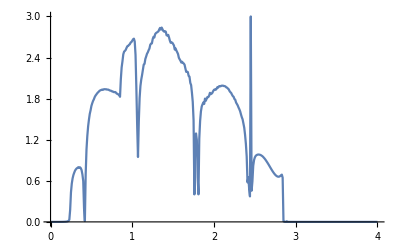

```mathematica
ListPlot[%18,Joined->True]
```

```mathematica
set[60]
```

```mathematica
tr60[ω_,ϵ1_]:=Module[{Tin=T1[1,7],T=ρ[1,7],imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},list={RandomSample[{imp,imp6,imp3,imp,imp,imp,imp,imp10,imp,imp13,imp,imp,imp,imp9,imp6,imp3,imp3,imp,imp,imp10,imp5,imp,imp,imp8,imp,imp,imp8,imp9,imp2,imp8,imp3,imp2,imp8,imp,imp,imp9,imp,imp1,imp,imp6,imp12,imp,imp9,imp13,imp3,imp,imp1,imp5,imp,imp9,imp11,imp,imp9,imp1,imp1,imp,imp,imp5,imp,imp3,imp10,imp8,imp14,imp,imp5,imp,imp5,imp13,imp1,imp14,imp,imp7,imp,imp1,imp9,imp13,imp10,imp10,imp4,imp6,imp,imp,imp5,imp6,imp7,imp7,imp6,imp,imp7,imp1,imp,imp13,imp3,imp4,imp1,imp,imp,imp,imp,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
tr60[1,0.7]
```

0.892559

```mathematica
set[70]
```

{imp11,imp5,imp10,imp8,imp12,imp8,imp8,imp4,imp5,imp1,imp11,imp5,imp13,imp7,imp11,imp,imp4,imp5,imp,imp8,imp13,imp,imp13,imp4,imp4,imp,imp8,imp1,imp6,imp3,imp11,imp9,imp,imp6,imp12,imp1,imp3,imp11,imp,imp8,imp13,imp,imp14,imp,imp4,imp1,imp12,imp9,imp,imp,imp4,imp11,imp,imp11,imp,imp,imp,imp8,imp12,imp,imp8,imp,imp,imp7,imp8,imp13,imp8,imp8,imp2,imp3,imp10,imp10,imp,imp13,imp6,imp1,imp7,imp8,imp13,imp,imp12,imp6,imp11,imp12,imp6,imp,imp10,imp,imp,imp,imp13,imp,imp,imp,imp9,imp13,imp,imp7,imp2,imp14}

```mathematica
tr70[ω_,ϵ1_]:=Module[{Tin=T1[1,7],T=ρ[1,7],imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},list={RandomSample[{imp11,imp5,imp10,imp8,imp12,imp8,imp8,imp4,imp5,imp1,imp11,imp5,imp13,imp7,imp11,imp,imp4,imp5,imp,imp8,imp13,imp,imp13,imp4,imp4,imp,imp8,imp1,imp6,imp3,imp11,imp9,imp,imp6,imp12,imp1,imp3,imp11,imp,imp8,imp13,imp,imp14,imp,imp4,imp1,imp12,imp9,imp,imp,imp4,imp11,imp,imp11,imp,imp,imp,imp8,imp12,imp,imp8,imp,imp,imp7,imp8,imp13,imp8,imp8,imp2,imp3,imp10,imp10,imp,imp13,imp6,imp1,imp7,imp8,imp13,imp,imp12,imp6,imp11,imp12,imp6,imp,imp10,imp,imp,imp,imp13,imp,imp,imp,imp9,imp13,imp,imp7,imp2,imp14}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
set[80]
```

{imp8,imp14,imp1,imp,imp7,imp1,imp7,imp,imp1,imp7,imp3,imp,imp8,imp2,imp,imp2,imp9,imp7,imp11,imp2,imp3,imp9,imp5,imp10,imp3,imp4,imp2,imp,imp2,imp,imp11,imp2,imp,imp9,imp9,imp13,imp14,imp,imp13,imp14,imp3,imp,imp11,imp,imp3,imp,imp,imp,imp,imp1,imp12,imp9,imp13,imp,imp8,imp5,imp8,imp2,imp14,imp1,imp4,imp8,imp5,imp10,imp4,imp9,imp14,imp7,imp4,imp6,imp8,imp11,imp8,imp5,imp8,imp7,imp7,imp7,imp2,imp12,imp6,imp2,imp7,imp14,imp14,imp6,imp7,imp12,imp2,imp1,imp1,imp12,imp4,imp,imp2,imp8,imp14,imp4,imp14,imp12}

```mathematica
tr80[ω_,ϵ1_]:=Module[{Tin=T1[1,7],T=ρ[1,7],imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},list={RandomSample[{imp8,imp14,imp1,imp,imp7,imp1,imp7,imp,imp1,imp7,imp3,imp,imp8,imp2,imp,imp2,imp9,imp7,imp11,imp2,imp3,imp9,imp5,imp10,imp3,imp4,imp2,imp,imp2,imp,imp11,imp2,imp,imp9,imp9,imp13,imp14,imp,imp13,imp14,imp3,imp,imp11,imp,imp3,imp,imp,imp,imp,imp1,imp12,imp9,imp13,imp,imp8,imp5,imp8,imp2,imp14,imp1,imp4,imp8,imp5,imp10,imp4,imp9,imp14,imp7,imp4,imp6,imp8,imp11,imp8,imp5,imp8,imp7,imp7,imp7,imp2,imp12,imp6,imp2,imp7,imp14,imp14,imp6,imp7,imp12,imp2,imp1,imp1,imp12,imp4,imp,imp2,imp8,imp14,imp4,imp14,imp12}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
set[90]
```

{imp14,imp4,imp,imp11,imp8,imp10,imp3,imp12,imp8,imp11,imp8,imp3,imp8,imp9,imp12,imp7,imp13,imp4,imp10,imp6,imp13,imp,imp3,imp10,imp11,imp8,imp6,imp1,imp6,imp3,imp3,imp,imp2,imp4,imp5,imp13,imp3,imp3,imp5,imp8,imp5,imp4,imp8,imp4,imp6,imp5,imp10,imp10,imp3,imp4,imp4,imp8,imp8,imp,imp7,imp1,imp8,imp5,imp5,imp4,imp8,imp2,imp9,imp6,imp6,imp,imp3,imp,imp13,imp6,imp9,imp2,imp6,imp8,imp2,imp12,imp1,imp11,imp9,imp3,imp5,imp6,imp12,imp12,imp8,imp,imp2,imp11,imp,imp7,imp1,imp12,imp11,imp1,imp10,imp3,imp10,imp6,imp13,imp14}

```mathematica
tr90[ω_,ϵ1_]:=Module[{Tin=T1[1,7],T=ρ[1,7],imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},list={RandomSample[{imp14,imp4,imp,imp11,imp8,imp10,imp3,imp12,imp8,imp11,imp8,imp3,imp8,imp9,imp12,imp7,imp13,imp4,imp10,imp6,imp13,imp,imp3,imp10,imp11,imp8,imp6,imp1,imp6,imp3,imp3,imp,imp2,imp4,imp5,imp13,imp3,imp3,imp5,imp8,imp5,imp4,imp8,imp4,imp6,imp5,imp10,imp10,imp3,imp4,imp4,imp8,imp8,imp,imp7,imp1,imp8,imp5,imp5,imp4,imp8,imp2,imp9,imp6,imp6,imp,imp3,imp,imp13,imp6,imp9,imp2,imp6,imp8,imp2,imp12,imp1,imp11,imp9,imp3,imp5,imp6,imp12,imp12,imp8,imp,imp2,imp11,imp,imp7,imp1,imp12,imp11,imp1,imp10,imp3,imp10,imp6,imp13,imp14}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Table[{ω,Mean[Table[tr50[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

$Aborted

```mathematica
Table[{ω,Mean[Table[tr60[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Table[{ω,Mean[Table[tr70[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Table[{ω,Mean[Table[tr80[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Table[{ω,Mean[Table[tr90[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```